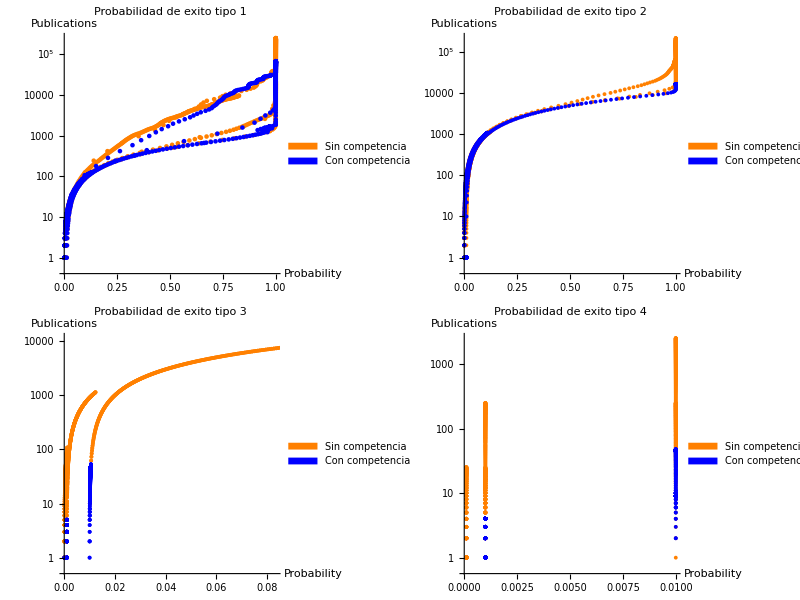

```mathematica
y = "/home/fabianact/ActualTesis/Tesis/ModelosPresentados/SinCompetencia";
x = "/home/fabianact/ActualTesis/Tesis/ModelosPresentados/ConCompetencia";
SetDirectory[y<>"/images"];
SetOptions[ListLogPlot,BaseStyle->{FontSize->18}];
pub1= Import[y<>"/averageResults/prob-pub-1-0.01-curve.csv"];
pub2= Import[y<>"/averageResults/prob-pub-1-0.001-curve.csv"];
pub3= Import[y<>"/averageResults/prob-pub-1-1.0E-4-curve.csv"];
pub4 = Import[y<>"/averageResults/prob-pub-5-0.01-curve.csv"];
pub5 = Import[y<>"/averageResults/prob-pub-5-0.001-curve.csv"];
pub6 = Import[y<>"/averageResults/prob-pub-5-1.0E-4-curve.csv"];
pub7= Import[x<>"/averageResults/prob-pub-1-0.01-100-true-curve.csv"];
pub8= Import[x<>"/averageResults/prob-pub-1-0.001-100-true-curve.csv"];
pub9= Import[x<>"/averageResults/prob-pub-1-1.0E-4-100-true-curve.csv"];
pub10= Import[x<>"/averageResults/prob-pub-5-0.01-100-true-curve.csv"];
pub11 = Import[x<>"/averageResults/prob-pub-5-0.001-100-true-curve.csv"];
pub12 = Import[x<>"/averageResults/prob-pub-5-1.0E-4-100-true-curve.csv"];
plotPub1= Legended[Show[ListLogPlot[{ pub1, pub2, pub3, pub4, pub5, pub6 },ImageSize->600, PlotStyle->{{Orange}}],ListLogPlot[{ pub7, pub8, pub9, pub10, pub11, pub12},ImageSize->600, PlotRange->All, PlotStyle->{{Blue}}],PlotLabel-> "Probabilidad de exito tipo 1",AxesLabel->{"Probability","Publications"}],Placed[SwatchLegend[{Orange,Blue},{Style["Sin competencia",12],Style["Con competencia",12]},LegendMargins->{{15,15},{5,5}},LegendFunction->Framed,LabelStyle->(FontFamily->"Helvetica")],{{0.5,0.1},{0,0}}]];

Export["prob-pub-1.png",plotPub1];

pub1= Import[y<>"/averageResults/prob-pub-2-0.01-curve.csv"];
pub2= Import[y<>"/averageResults/prob-pub-2-0.001-curve.csv"];
pub3= Import[y<>"/averageResults/prob-pub-2-1.0E-4-curve.csv"];
pub4 = Import[y<>"/averageResults/prob-pub-6-0.01-curve.csv"];
pub5 = Import[y<>"/averageResults/prob-pub-6-0.001-curve.csv"];
pub6 = Import[y<>"/averageResults/prob-pub-6-1.0E-4-curve.csv"];
pub7= Import[x<>"/averageResults/prob-pub-2-0.01-100-true-curve.csv"];
pub8= Import[x<>"/averageResults/prob-pub-2-0.001-100-true-curve.csv"];
pub9= Import[x<>"/averageResults/prob-pub-2-1.0E-4-100-true-curve.csv"];
pub10= Import[x<>"/averageResults/prob-pub-6-0.01-100-true-curve.csv"];
pub11 = Import[x<>"/averageResults/prob-pub-6-0.001-100-true-curve.csv"];
pub12 = Import[x<>"/averageResults/prob-pub-6-1.0E-4-100-true-curve.csv"];
plotPub2= Legended[Show[ListLogPlot[{ pub1, pub2, pub3, pub4, pub5, pub6 },ImageSize->600, PlotStyle->{{Orange}}],ListLogPlot[{ pub7, pub8, pub9, pub10, pub11, pub12},ImageSize->600, PlotRange->All, PlotStyle->{{Blue}}],PlotLabel-> "Probabilidad de exito tipo 2",AxesLabel->{"Probability","Publications"}],Placed[SwatchLegend[{Orange,Blue},{Style["Sin competencia",12],Style["Con competencia",12]},LegendMargins->{{15,15},{5,5}},LegendFunction->Framed,LabelStyle->(FontFamily->"Helvetica")],{{0.5,0.1},{0,0}}]];
Export["prob-pub-2.png",plotPub2];

pub1= Import[y<>"/averageResults/prob-pub-3-0.01-curve.csv"];
pub2= Import[y<>"/averageResults/prob-pub-3-0.001-curve.csv"];
pub3= Import[y<>"/averageResults/prob-pub-3-1.0E-4-curve.csv"];
pub4 = Import[y<>"/averageResults/prob-pub-3-0.01-curve.csv"];
pub5 = Import[y<>"/averageResults/prob-pub-3-0.001-curve.csv"];
pub6 = Import[y<>"/averageResults/prob-pub-3-1.0E-4-curve.csv"];
pub7= Import[x<>"/averageResults/prob-pub-7-0.01-100-true-curve.csv"];
pub8= Import[x<>"/averageResults/prob-pub-7-0.001-100-true-curve.csv"];
pub9= Import[x<>"/averageResults/prob-pub-7-1.0E-4-100-true-curve.csv"];
pub10= Import[x<>"/averageResults/prob-pub-7-0.01-100-true-curve.csv"];
pub11 = Import[x<>"/averageResults/prob-pub-7-0.001-100-true-curve.csv"];
pub12 = Import[x<>"/averageResults/prob-pub-7-1.0E-4-100-true-curve.csv"];
plotPub3= Legended[Show[ListLogPlot[{ pub1, pub2, pub3, pub4, pub5, pub6 },ImageSize->600, PlotStyle->{{Orange}}],ListLogPlot[{ pub7, pub8, pub9, pub10, pub11, pub12},ImageSize->600, PlotRange->All, PlotStyle->{{Blue}}],PlotLabel-> "Probabilidad de exito tipo 3",AxesLabel->{"Probability","Publications"}],Placed[SwatchLegend[{Orange,Blue},{Style["Sin competencia",12],Style["Con competencia",12]},LegendMargins->{{15,15},{5,5}},LegendFunction->Framed,LabelStyle->(FontFamily->"Helvetica")],{{0.5,0.1},{0,0}}]];
Export["prob-pub-3.png",plotPub3];

pub1= Import[y<>"/averageResults/prob-pub-4-0.01-curve.csv"];
pub2= Import[y<>"/averageResults/prob-pub-4-0.001-curve.csv"];
pub3= Import[y<>"/averageResults/prob-pub-4-1.0E-4-curve.csv"];
pub4 = Import[y<>"/averageResults/prob-pub-8-0.01-curve.csv"];
pub5 = Import[y<>"/averageResults/prob-pub-8-0.001-curve.csv"];
pub6 = Import[y<>"/averageResults/prob-pub-8-1.0E-4-curve.csv"];
pub7= Import[x<>"/averageResults/prob-pub-4-0.01-100-true-curve.csv"];
pub8= Import[x<>"/averageResults/prob-pub-4-0.001-100-true-curve.csv"];
pub9= Import[x<>"/averageResults/prob-pub-4-1.0E-4-100-true-curve.csv"];
pub10= Import[x<>"/averageResults/prob-pub-8-0.01-100-true-curve.csv"];
pub11 = Import[x<>"/averageResults/prob-pub-8-0.001-100-true-curve.csv"];
pub12 = Import[x<>"/averageResults/prob-pub-8-1.0E-4-100-true-curve.csv"];
plotPub4= Legended[Show[ListLogPlot[{ pub1, pub2, pub3, pub4, pub5, pub6 },ImageSize->600, PlotStyle->{{Orange}}],ListLogPlot[{ pub7, pub8, pub9, pub10, pub11, pub12},ImageSize->600, PlotRange->All, PlotStyle->{{Blue}}],PlotLabel-> "Probabilidad de exito tipo 4",AxesLabel->{"Probability","Publications"}],Placed[SwatchLegend[{Orange,Blue},{Style["Sin competencia",12],Style["Con competencia",12]},LegendMargins->{{15,15},{5,5}},LegendFunction->Framed,LabelStyle->(FontFamily->"Helvetica")],{{0.5,0.1},{0,0}}]];
Export["prob-pub-4.pdf",plotPub4];

pubTotal=Grid[{{plotPub1,plotPub2},{plotPub3,plotPub4}}]
Export["prob-pub-total-100-true.png",pubTotal];
```